## Legend for coloring

Flow of the discussion and labels for the action being performed.

Technical comments (mostly on the Mathematica commands).

Comments and thoughts on what we are seeing.

## Technical Setup

Define some system-specific variables here - e.g. the base path for where the data files are stored. For some reason, Mathematica does not import the file successfully if it’s just located in the same folder and the path is omitted.

```mathematica
pathBase="/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/";
```

Define function functions for accessing the data. Note that these functions (or most of them) do not work over the index but over the row itself provided as an argument. That is because functions such as Select in Mathematica provide for that.

First some functions to be used in the Select clause to pick out subjects and codes.

```mathematica
isSubject[subjid_,r_]:=r[[1]]==subjid; (* checks if the given row belongs to the given subject *)
isImgCode[code_,r_]:=r[[2]]==code;
```

Next, some functions to select the code for the subject.

```mathematica
vector[r_]:=r[[3;;Length[r]]]; (* used to get just the MEB from the row; the first 3 entries are metadata such as subjid and imgcode *)
quantize[x_]:=If[x>0.0,1,0]; (* quantize a single number *)
quantizedVector[r_]:=vector[r];(*THIS IS A PART I HAVE CHANGE TO REMOVE THE QUANTIZATION!!*) (* return the quantized MEB for the row *)
targetForSubject[subjid_,data_]:=(quantizedVector/@Select[data,isSubject[subjid,#]&&isImgCode["fa",#]&])[[1]];  (* find the real MEB of the given subject; returns just a single list *);
imgCodeVectorForSubject[subj_,code_,data_]:=quantizedVector[Select[data,isSubject[subj,#]&&isImgCode[code,#]&][[1]]]
```

```mathematica
data=Import["howfar_vgg_printcodes_subject_00070_with_imposter.csv",Path->pathBase]
```

{1}
 |  |  |  |

```mathematica
EuclideanDistance[vector[data[[1]]],vector[data[[2]]]]
```

40.7746

```mathematica
Length[data]
```

618

Here are some functions to compute the distance between the fa and the fb/rc for a subject.

```mathematica
faFbDist[subj_,data_]:=EuclideanDistance[imgCodeVectorForSubject[subj,"fa",data],imgCodeVectorForSubject[subj,"fb",data]];
faRcDist[subj_,data_]:=EuclideanDistance[imgCodeVectorForSubject[subj,"fa",data],imgCodeVectorForSubject[subj,"rc",data]];
faFbDiffSubjDist[subj1_,subj2_,data_]:=EuclideanDistance[imgCodeVectorForSubject[subj1,"fa",data],imgCodeVectorForSubject[subj2,"fb",data]];
faRcDiffSubjDist[subj1_,subj2_,data_]:=EuclideanDistance[imgCodeVectorForSubject[subj1,"fa",data],imgCodeVectorForSubject[subj2,"rc",data]];
distSubjCodes[subj_,code1_,code2_,data_]:=EuclideanDistance[imgCodeVectorForSubject[subj,code1,data],imgCodeVectorForSubject[subj,code2,data]];
distDiffSubjectsForCodes[subj1_,subj2_,code1_,code2_,data_]:=EuclideanDistance[imgCodeVectorForSubject[subj1,code1,data],imgCodeVectorForSubject[subj2,code2,data]];
```

These functions get some listing of subjects that we can work with for the evaluation, including imposter pairs and such.

```mathematica
allsubjectsSorted[data_]:=Sort[DeleteDuplicates[data[[All,1]]]]; (* gets a list of all subjects in a sorted order *)
allsubjectsShuffled[data_]:=RandomSample[allsubjectsSorted[data]]; (* gets a list of all subjects in a SHUFFLED order, used for imposter generation *)
imposterPairs[data_]:=Table[{(allsubjectsSorted[data])[[i]],(allsubjectsShuffled[data])[[i]]},{i, 1,Length[allsubjectsSorted[data]]}];
allSubjectsWithCode[data_,code_]:=Sort[Select[data,isImgCode[code,#]&][[All,1]]];
imposterParisForSubjectsWithCode[data_,code_]:=(
Clear[subj,imp];
subj=allSubjectsWithCode[data,code];
imp=RandomSample[subj];
Table[{subj[[i]],imp[[i]]},{i,1,Length[subj]}]
);
imposterParisForSubjectsWithCodeWithSpecificImposterPairs[data_,code_,pairs_]:=(
Table[{pairs[[i,1]],pairs[[i,2]]},{i,1,Length[subj]}]
);
```

These functions generate the fa/fb and the fa/rc distances for all subjects.

```mathematica
allFaFbDistances[subjects_,data_]:=faFbDist[#,data]&/@subjects;
allFaRcDistances[subjects_,data_]:=faRcDist[#,data]&/@subjects;
allDistancesForCode[subjects_,code_,data_]:=distSubjCodes[#,"fa",code,data]&/@subjects;
```

Finally, these functions give us the data in a format of tuples of the form (subjid, genuine_score, imposterid, imposter_score). The imposters are chosen randomly in each run.

```mathematica
genuineAndImposterDataInTuples[subjectPairs_,genuineScores_,imposterScores_]:=Table[{(subjectPairs[[All,1]])[[i]],genuineScores[[i]],(subjectPairs[[All,2]])[[i]],imposterScores[[i]]},{i,Length[subjectPairs]}]
```

```mathematica
allGenuineAndImposterScoresFromData[data_,code_]:=(
Clear[pairs]; 
pairs=imposterParisForSubjectsWithCode[data,code];
genuineAndImposterDataInTuples[pairs,allDistancesForCode[pairs[[All,1]],code,data], ((distDiffSubjectsForCodes[#[[1]],#[[2]],"fa",code,data]&)/@(pairs))]);
allGenuineAndImposterScoresFromDataForSpecificPairs[data_,code_,pairs_]:=(
Clear[pairsLoc]; 
pairsLoc=imposterParisForSubjectsWithCodeWithSpecificImposterPairs[data,code,pairs];
genuineAndImposterDataInTuples[pairs,allDistancesForCode[pairs[[All,1]],code,data], ((distDiffSubjectsForCodes[#[[1]],#[[2]],"fa",code,data]&)/@(pairs))])
```

More functions to calculate the confusion matrix, GAR’s, FAR’s, etc. -- these will work with data in the format output by allGenuineAndImposterScoresFromData, i.e. the 4-tuple format.

```mathematica
genuineScores[resultsTuplesData_]:=resultsTuplesData[[All,2]];
imposterScores[resultsTuplesData_]:=resultsTuplesData[[All,4]];
truePositive[resultsTuplesData_,threshold_]:=Fold[If[#2<threshold,#1+1,#1]&,0,genuineScores[resultsTuplesData]];
falseNegative[resultsTuplesData_,threshold_]:=Fold[If[#2>=threshold,#1+1,#1]&,0,genuineScores[resultsTuplesData]];
trueNegative[resultsTuplesData_,threshold_]:=Fold[If[#2>=threshold,#1+1,#1]&,0,imposterScores[resultsTuplesData]];
falsePositive[resultsTuplesData_,threshold_]:=Fold[If[#2<threshold,#1+1,#1]&,0,imposterScores[resultsTuplesData]];
gar[resultsTuplesData_,threshold_]:=truePositive[resultsTuplesData,threshold]/Length[resultsTuplesData];
far[resultsTuplesData_,threshold_]:=falsePositive[resultsTuplesData,threshold]/Length[resultsTuplesData];
frr[resultsTuplesData_,threshold_]:=falseNegative[resultsTuplesData,threshold]/Length[resultsTuplesData];
```

```mathematica
garAt0Far[resultsTuplesData_]:=(
Clear[allscores,garsList,farsList,garFarPairs,only0Fars];
allscores=Join[genuineScores[resultsTuplesData],imposterScores[resultsTuplesData]];
garsList=gar[resultsTuplesData,#]&/@allscores;
farsList=far[resultsTuplesData,#]&/@allscores;
garFarPairs=Table[{garsList[[i]],farsList[[i]],allscores[[i]]},{i,1,Length[allscores]}];
only0Fars=Select[garFarPairs,#[[2]]<0.0000001&];
N[Max[only0Fars[[All,1]]]]
)
```

The EER function will return the result in the format (frr, far, diff).

```mathematica
eer[resultsTuplesData_]:=(
Clear[allscores,frrsList,farsList,frrFarDiffTriples,minDiff];
allscores=Join[genuineScores[resultsTuplesData],imposterScores[resultsTuplesData]];
frrsList=frr[resultsTuplesData,#]&/@allscores;
farsList=far[resultsTuplesData,#]&/@allscores;
frrFarDiffTriples=Table[{frrsList[[i]],farsList[[i]],Abs[frrsList[[i]]-farsList[[i]]]},{i,1,Length[allscores]}];
minDiff=Min[frrFarDiffTriples[[All,3]]];
N[DeleteDuplicates[Select[frrFarDiffTriples,#[[3]]==minDiff&]]][[1]]
)
```

```mathematica
rocCurvePoints[resultsTuplesData_]:=(
Clear[allscores,garsList,frrsList,garFrrPairs];
allscores=Join[genuineScores[resultsTuplesData],imposterScores[resultsTuplesData]];
garsList=gar[resultsTuplesData,#]&/@allscores;
frrsList=far[resultsTuplesData,#]&/@allscores;
garFrrPairs=Table[{frrsList[[i]],garsList[[i]]},{i,1,Length[allscores]}];
garFrrPairs
)
```

This function will help with generating the analysis tuples and saving them to a file (so that when we generate random imposters, we save off the imposter pairs to a file and can later reproduce our results).

```mathematica
analysisTuples[data_,code_,filename_]:=(
Clear[tup];
tup=allGenuineAndImposterScoresFromData[fullData,code];
Export[pathBase<>"/mathematica-exports/"<>filename,tup, Path->pathBase];
tup
); (*I have added a /mathematica-exports/ folder here in order to keep this form overwriting previous data when the notebook is evaluated from scratch.*)
analysisTuplesWithSpecificPairs[data_,code_,filename_,pairs_]:=(
Clear[tup];
tup=allGenuineAndImposterScoresFromDataForSpecificPairs[fullData,code,pairs];
Export[pathBase<>"/mathematica-exports/"<>filename,tup, Path->pathBase];
tup
);
```

### Pick a Pair, any Pair

Here I will standardize several sets of imposter pairs to work with.

```mathematica
producePairsFromExportedData[exportedAnalyzedData_]:=Table[{exportedAnalyzedData[[i,1]],exportedAnalyzedData[[i,3]]},{i,1,Length[exportedAnalyzedData]}];
```

```mathematica
pairsRCList1=producePairsFromExportedData[Import["data_imposter_and_genuine_tuples_for_quantized_vgg_for_rc_subjects.csv",Path->pathBase,HeaderLines->0]];
```

```mathematica
pairsRCList2=producePairsFromExportedData[Import["data_imposter_and_genuine_tuples_for_quantized_vgg_for_rc_subjects_2.csv",Path->pathBase,HeaderLines->0]];
```

```mathematica
pairsFBList1=producePairsFromExportedData[Import["data_imposter_and_genuine_tuples_for_quantized_vgg_for_fb_subjects.csv",Path->pathBase,HeaderLines->0]];
```

### Analysis

```mathematica
fullData=Import["vgg_output_one_img_per_type_per_subject.csv",Path->pathBase,HeaderLines->1];
```

```mathematica
analyzedDataRCs=allGenuineAndImposterScoresFromDataForSpecificPairs[fullData,"rc",pairsRCList2];
```

```mathematica
garAt0Far[analyzedDataRCs]
```

0.899522

```mathematica
eer[analyzedDataRCs]
```

{0.0406699,0.0406699,0.}

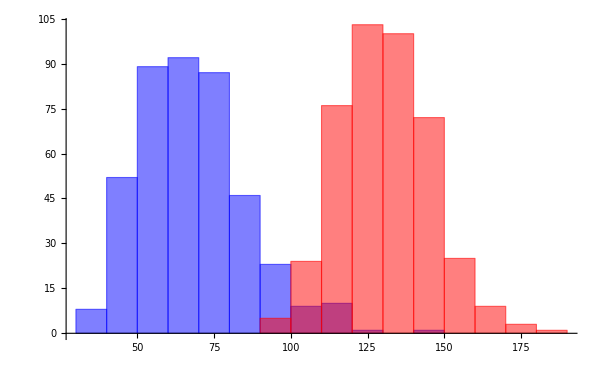

```mathematica
Histogram[{analyzedDataRCs[[All,2]],analyzedDataRCs[[All,4]]},ChartStyle->{Blue,Red},]
```

```mathematica
analyzedDataFBs=allGenuineAndImposterScoresFromDataForSpecificPairs[fullData,"fb",pairsFBList1];
```

```mathematica
garAt0Far[analyzedDataFBs]
```

0.964029

```mathematica
eer[analyzedDataFBs]
```

{0.0191847,0.0191847,0.}

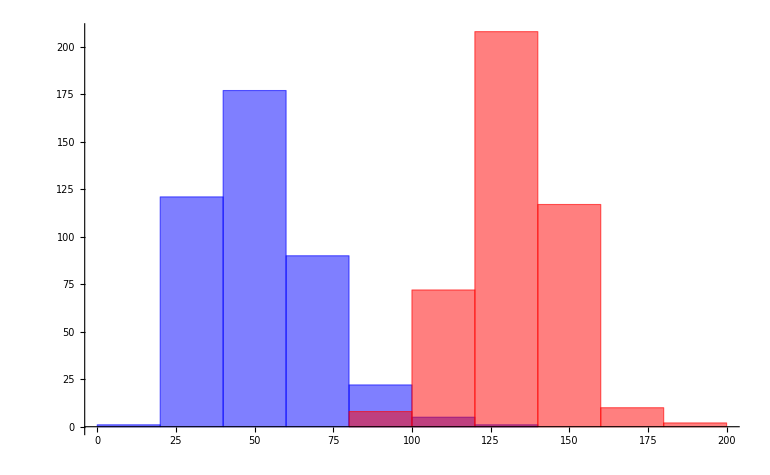

```mathematica
Histogram[{analyzedDataFBs[[All,2]],analyzedDataFBs[[All,4]]},ChartStyle->{Blue,Red}]
```

```mathematica
rocPointsFbs=rocCurvePoints[analyzedDataFBs];
```

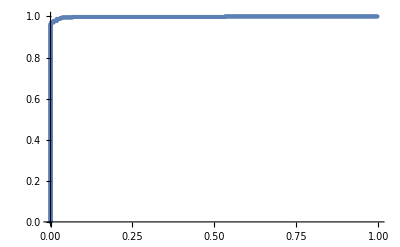

```mathematica
ListPlot[rocPointsFbs]
```

```mathematica
rocPointsRcs=rocCurvePoints[analyzedDataRCs];
```

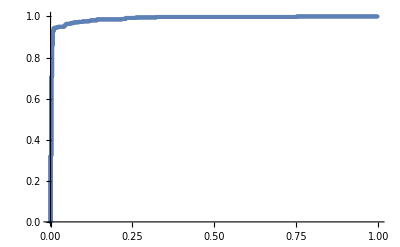

```mathematica
ListPlot[rocPointsRcs]
```

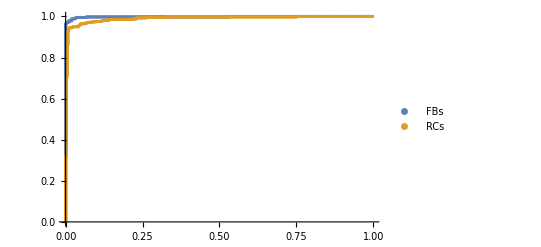

```mathematica
ListPlot[{rocPointsFbs,rocPointsRcs},PlotLegends->{"FBs","RCs"}]
```

```mathematica
Length[pairsFBList1]
```

417

```mathematica
Length[pairsRCList1]
```

418

```mathematica
Length[pairsRCList2]
```

418